```mathematica
f[x_]:=A √x BesselK[ⅈ √(b-(1/4)),k x]
```

```mathematica
FullSimplify[f''[x]+b/x^2 f[x]-k^2 f[x]==0]
```

True

```mathematica
h[x_]:=√x BesselK[4ⅈ,x]
```

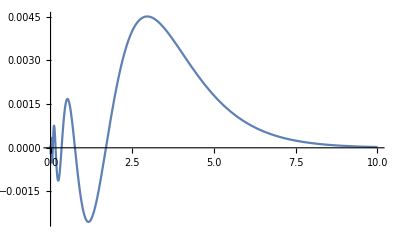

```mathematica
Plot[h[x],{x,0,10}]
```

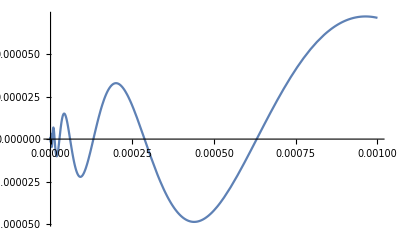

```mathematica
Plot[h[x],{x,0,.001}]
```

```mathematica
Integrate[(f[x])^2,{x,0,∞}]
```

ConditionalExpression[(A^2 √(-1+4 b) π Csch[√(-1/4+b) π])/(4 k^2), -2<Im[√(-1+4 b)]<2&&Re[k]>0]

```mathematica
h[x_]:=√x BesselK[4ⅈ,x]
```

```mathematica
FindRoot[h[x]==0,{x,2}]
```

{x→1.69541+0. ⅈ}

```mathematica
{x->1.6954066933505485+0. ⅈ}
```

{x→1.69541+0. ⅈ}

```mathematica
j[x_]:=If[x≥1,h[1.6954066933505485x],0]
```

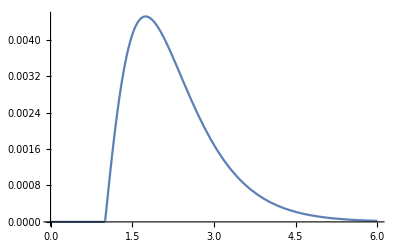

```mathematica
Plot[j[x],{x,0,6}]
```